## 7/3 Progress

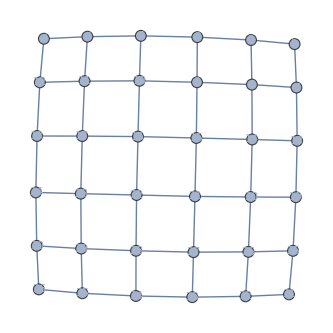

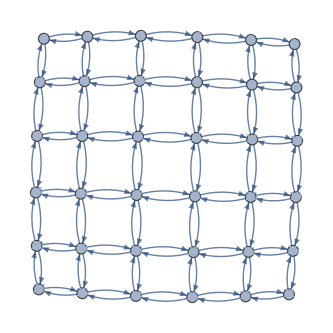

```mathematica
squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[i*n+j<-> i*n+j+1, {j, 1, n-1}], {i, 0, n-1}], Table[Table[i*n+j<-> i*n+j+n, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25, EdgeWeight->{_->1}];

squareDirectedGraph[n_Integer]:=
Graph[Flatten[{Table[Table[{i*n+j-> i*n+j+1, i*n+j+1-> i*n+j}, {j, 1, n-1}], {i, 0, n-1}], Table[Table[{i*n+j-> i*n+j+n, i*n+j+n-> i*n+j}, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25];

myGraph = squareGraph[6]
myDirectedGraph = squareDirectedGraph[6]
```

I made two visualization of a common road structure in cities: a grid like structure of “blocks” of approximately equal length roads. The intersections, which can be marked by traffic lights, are labeled from 1 to 36 and serve as the nodes, while the edges are the roads. The undirected graph above is similar to the directed graph below because splitting a bi-directional road into two equal but opposite directions are essentially equal.

I played with some formatting too, including making sure that the edges are weighted with 1, but not labeled (or else it will look too disgusting). I also aligned the vertex number label to be centered and vertex size to be 1/4 of its intended size. 

The generation involves two nested Table structures, joined by Flatten. The first nest runs through all but the right column of the grid to generate horizontal edges, and ths

```mathematica
findLengthKPath[k_Integer, st_Integer, g_]:=
Module[{rando := RandomSample[Range[VertexCount[g]]]},
candidatePaths = Table[FindPath[g, st, rando[[i]], {k}], {i, 1, VertexCount[g]}];
Select[candidatePaths, Length[#]>0&, 1]
]
```

{1,2,3,4,5,6,12,11,17,18,24}

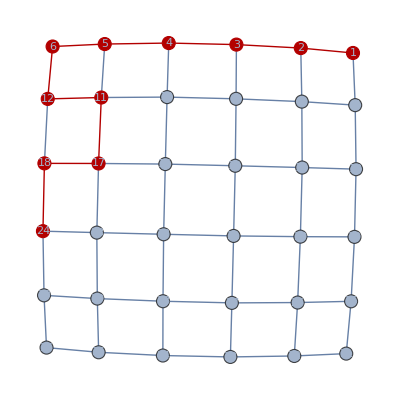

```mathematica
foundPath = Flatten[findLengthKPath[10, 1]]
HighlightGraph[myGraph, PathGraph[foundPath]]
```

## 7/4 Progress

```mathematica
findLengthKCycle[k_Integer, st_Integer, g_]:=
Module[{rando := RandomSample[FindCycle[{g, st}, {k}, All]]},
rando[[1]]
]
```

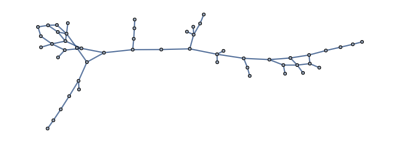

{48<->47,47<->43,43<->44,44<->39,39<->31,31<->32,32<->40,40<->41,41<->50,50<->49,49<->48}

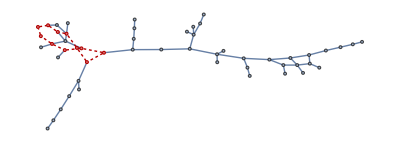

```mathematica
randomG = Graph[{1<->2,2<->3,3<->4, 4<->5, 5<->6, 6<->7, 6<->9, 5<->8, 8<->9, 9<->10, 8<->11, 11<->12, 9<->12, 12<->13, 11<->14, 14<->15, 15<->16, 14<->17, 17<->18, 17<->19, 17<->20, 20<->21, 21<->22, 21<->23, 21<->24, 24<->25, 20<->26, 26<->27, 27<->28, 28<->29, 29<->30, 27<->31, 31<->32, 32<->33, 33<->34, 33<->35, 35<->36, 36<->37, 37<->38, 31<->39, 32<->40, 39<->40, 40<->41, 41<->42, 39<->42, 42<->43, 43<->44, 39<->44, 44<->45, 43<->46, 43<->47, 47<->48, 48<->49, 49<->50, 42<->50, 41<->50, 49<->51, 41<->51, 41<->52}]

foundCycle = findLengthKCycle[11, 48, randomG]
HighlightGraph[randomG, PathGraph[foundCycle], GraphHighlightStyle->"Dotted"]
```

```mathematica
GeoGraphPlot[{GeoPosition[{50,60.1}]<->GeoPosition[{50.125,59.1}]}, GraphLayout->"Walking"]
```

Made a neat little function that takes a cycle length, starting node, and graph, and draws out the cycle.

Figured out GeoGraphPlot can take two GeoPositions connected by an edge, and help “walk” through the two edges.

## 7/7 Progress